```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
```

```mathematica
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

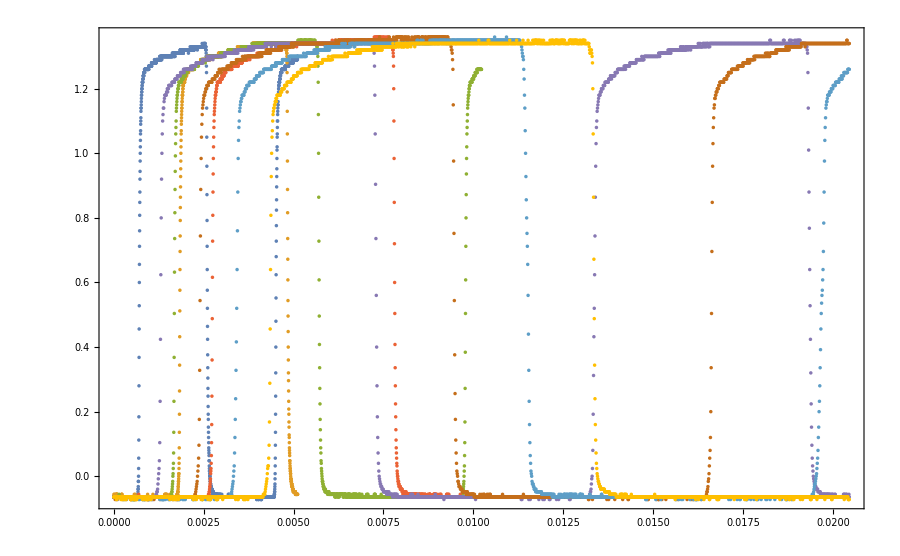

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[8],ImageSize->900,Frame->True]
```

```mathematica
fitdata =Select[filterdata[[8, 1]], #[[1]]≥ 0 && #[[1]]≤0.012&];
nlm= NonlinearModelFit[fitdata,{ a/(1+Exp[(-x+μ)/σ])+b-Piecewise[{{0,x<μ},{ c Exp[-d x],x≥μ}}],a<10,b<0,b>-0.1,c>0,c<3,d>0,d<1000,σ>0,σ<0.0001,μ<0.005,μ>0.004}, {{a,2},{b,-0.07},{μ,0.0043},{σ,0.00003},{c,2},{d,500}}, x]
nlm["ParameterTable"]
```

FittedModel[-0.0640735+1.41143/(1+ⅇ^(58038.6 («21»-x)))-(Piecewise[{{0, x<0.00435538}, {3. ⅇ^(-651.414 x), x≥0.00435538}, {0, True}}])]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.41143 | 0.000733614 | 1923.94 | 2.49986032316×10^-2088
b | -0.0640735 | 0.000407929 | -157.07 | 3.1214321543×10^-800
μ | 0.00435538 | 2.01554×10^-7 | 21609. | 1.58625022751×10^-3343
σ | 0.0000172299 | 1.79639×10^-7 | 95.9143 | 1.18991950225×10^-563
c | 3. | 0.164075 | 18.2843 | 4.81439×10^-66
d | 651.414 | 11.4957 | 56.6658 | 6.94403044307×10^-341

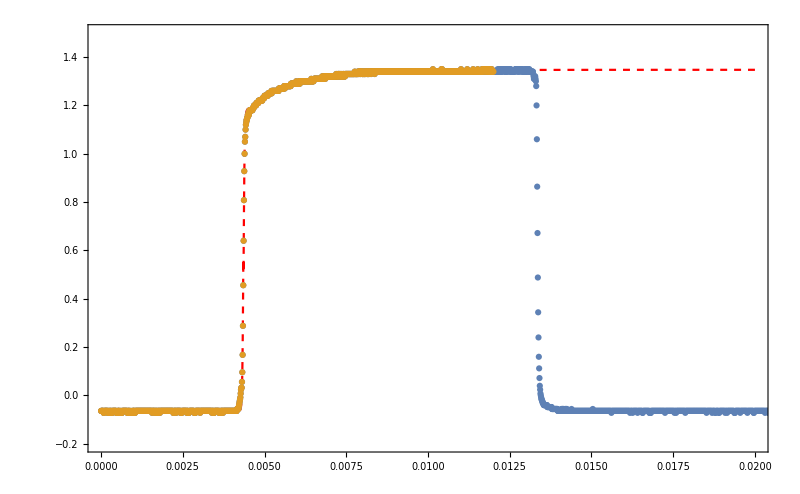

```mathematica
Show[Plot[Normal[nlm],{x,0,0.02},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed}],ListPlot[{filterdata[[8,1]],fitdata}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm], c/(1+Exp[(-x+0.0043)/0.00003])-0.06-Piecewise[{{0,x<0.0043},{a Exp[-b x],x≥0.0043}}]},{x,0,0.02},ImageSize->800,Frame->True,PlotRange->{-0.2,3},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed}],ListPlot[{filterdata[[8,1]],fitdata}]],{a,1,10},{b,0,1000},{c,1,5}]
```

```mathematica
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
```

```mathematica
?UnitStep
```

RowBox[{"UnitStep", "[", StyleBox["x", "TI"], "]"}] represents the unit step function, equal to 0 for RowBox[{StyleBox["x", "TI"], "<", "0"}] and 1 for RowBox[{StyleBox["x", "TI"], "≥", "0"}]. 
RowBox[{"UnitStep", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional unit step function which is 1 only if none of the SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] are negative.

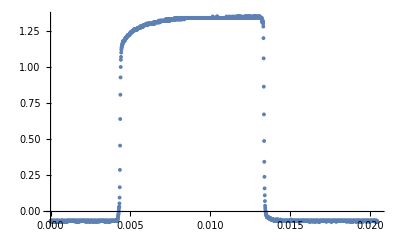

```mathematica
ListPlot[filterdata[[8,1]]]
```

```mathematica
Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.